## Fitting sigma dan eden

### Memisahkan data Pr vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\efpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\efpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\efpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[3]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\efpc_gup1E-9.dat

### Memisahkan data σ (= Pr-Pt) vs ED dlm 1 file tersendiri

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP0.E+00.dat"}],{Number,Number,Number,Number,Number,Number}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\sfpc_gup0E0.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-07.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\sfpc_gup1E-7.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-08.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\sfpc_gup1E-8.dat

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"EOS_FSU2HZ2_GUP1.E-09.dat"}],{Number,Number,Number,Number,Number,Number}];
Export[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],Transpose[{Transpose[data][[5]],Transpose[data][[5]]-Transpose[data][[6]]}]]
```

E:\Dropbox\Riset-riset\00 Serrano-Liska TOV anisotropik\NUMERIK_alka\2022-03-03Cek\file_alka_cek_2022-03-15\fitting\sfpc_gup1E-9.dat

### fitting anisotropik

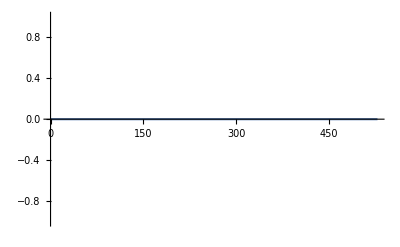

0.

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup0E0.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]}(*,Epilog->{PointSize[0.02],Map[Point,data]}*),PlotRange->Full]
```

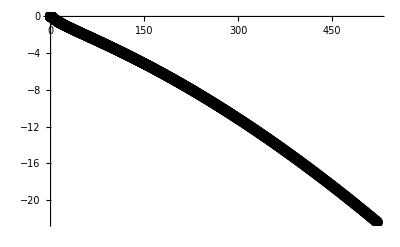

-0.025289589767689545 - 0.043871416138754185*P0 + 
     -  0.00019765635295503786*P0**2 - 1.3879637310689232e-6*P0**3 + 
     -  4.269131577141152e-9*P0**4 - 6.426655315449915e-12*P0**5 + 
     -  3.768403301516009e-15*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-7.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

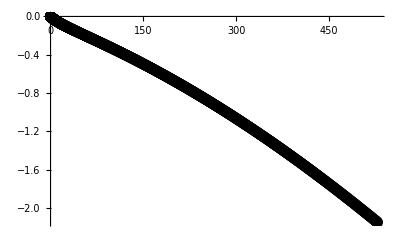

-0.00458706666936496 - 0.004220466683227455*P0 + 
     -  0.000018778181142047565*P0**2 - 
     -  1.3025426320458175e-7*P0**3 + 3.979182166343163e-10*P0**4 - 
     -  5.941766163599393e-13*P0**5 + 3.4541912747099285e-16*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-8.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

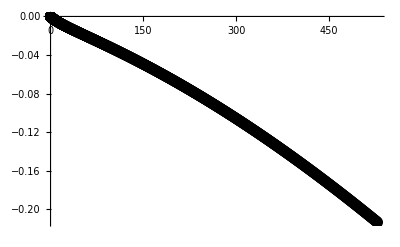

-0.0004780677905505392 - 0.0004204666885422772*P0 + 
     -  1.869018153246078e-6*P0**2 - 1.2951117047529519e-8*P0**3 + 
     -  3.9547110429565084e-11*P0**4 - 5.901970618889158e-14*P0**5 + 
     -  3.429024018047249e-17*P0**6

```mathematica
data=ReadList[FileNameJoin[{NotebookDirectory[],"sfpc_gup1E-9.dat"}],{Number,Number}];
fitted=Fit[data,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
FortranForm[fitted]
Plot[fitted,{P0,Min[Transpose[data][[1]]],Max[Transpose[data][[1]]]},Epilog->{PointSize[0.02],Map[Point,data]}]
```

### fitting energy density GUP 0E0

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 0E0 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup0E0.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={dataOuterCore[[1]],dataOuterCore[[2]]};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

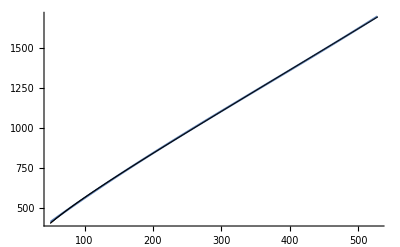

254.572+3.27227 P0-0.00199025 P0^2+1.84396×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP0E0=fitted
```

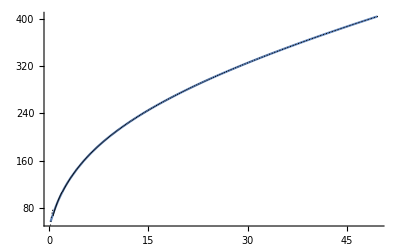

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16,P0^17},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP0E0=fitted;
```

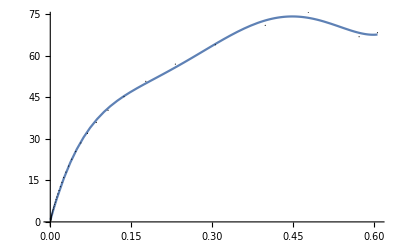

0.426006+714.24 P0-4571.21 P0^2+16153.3 P0^3-26410.3 P0^4+15662.1 P0^5

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4,P0^5},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP0E0=fitted
```

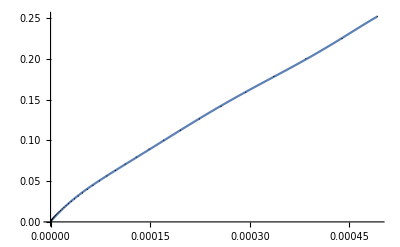

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP0E0=fitted
```

#### Cek hasilnya

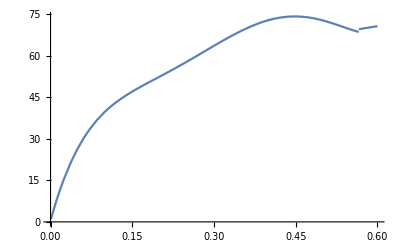

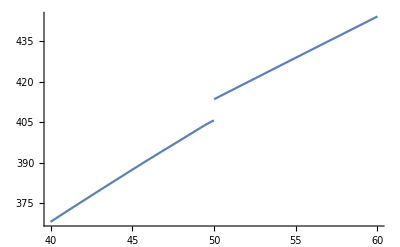

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP0E0;
FED2[P0_]=fitOuterCoreGUP0E0;
FED3[P0_]=fitInnerCrustGUP0E0;
FED4[P0_]=fitOuterCrustGUP0E0;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP0E0//FortranForm
```

254.57247440600344 + 3.2722668135019894*P0 - 
     -  0.0019902480708849034*P0**2 + 1.8439627167238033e-6*P0**3

```mathematica
fitOuterCoreGUP0E0//FortranForm
```

49.267245301992 + 39.12015287002968*P0 - 
     -  6.020094633721215*P0**2 + 0.3441152374080011*P0**3 + 
     -  0.1885554331444731*P0**4 - 0.06637720355881765*P0**5 + 
     -  0.011475525194044604*P0**6 - 0.0012852136878535097*P0**7 + 
     -  0.00010121502625294346*P0**8 - 
     -  5.817713041305554e-6*P0**9 + 2.485435214623891e-7*P0**10 - 
     -  7.942609315374174e-9*P0**11 + 
     -  1.8917771422067206e-10*P0**12 - 
     -  3.3098276551326267e-12*P0**13 + 
     -  4.129626534967556e-14*P0**14 - 
     -  3.477346789547739e-16*P0**15 + 
     -  1.770739061738443e-18*P0**16 - 4.11819633746566e-21*P0**17

```mathematica
fitInnerCrustGUP0E0//FortranForm
```

0.4260064795640439 + 714.2395621878875*P0 - 
     -  4571.210848278883*P0**2 + 16153.315408750519*P0**3 - 
     -  26410.273422294766*P0**4 + 15662.087088271082*P0**5

```mathematica
fitOuterCrustGUP0E0//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em7

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em7 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-7.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

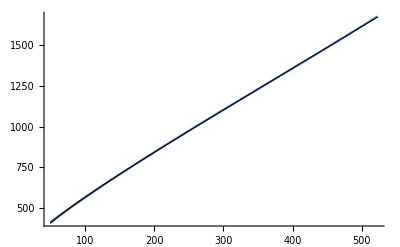

253.632+3.27521 P0-0.00204754 P0^2+1.90427×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em7=fitted
```

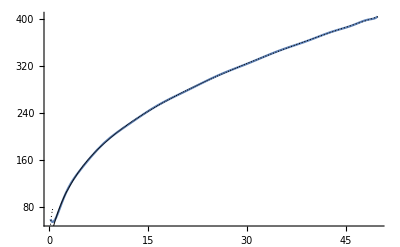

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em7=fitted;
```

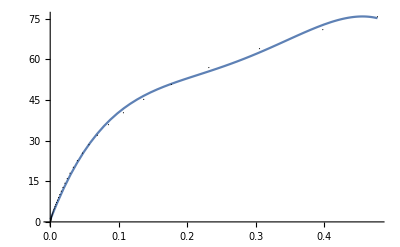

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em7=fitted
```

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em7=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

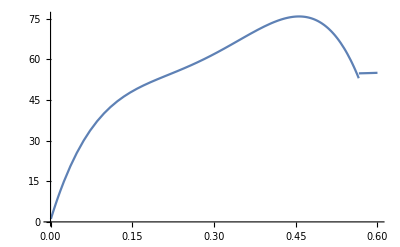

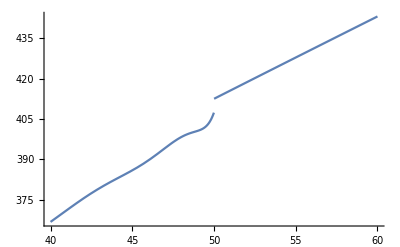

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em7;
FED2[P0_]=fitOuterCoreGUP1Em7;
FED3[P0_]=fitInnerCrustGUP1Em7;
FED4[P0_]=fitOuterCrustGUP1Em7;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em7//FortranForm
```

253.6316521603898 + 3.2752062368565222*P0 - 
     -  0.0020475370384748586*P0**2 + 1.9042736185326143e-6*P0**3

```mathematica
fitOuterCoreGUP1Em7//FortranForm
```

66.96695430515722 - 56.51414470005744*P0 + 
     -  80.53182092659665*P0**2 - 38.23653809705289*P0**3 + 
     -  10.427869506304706*P0**4 - 1.8375616323890898*P0**5 + 
     -  0.22236002007323272*P0**6 - 0.019184652205875004*P0**7 + 
     -  0.0012083962470858635*P0**8 - 
     -  0.0000563245410342902*P0**9 + 
     -  1.9522095644462132e-6*P0**10 - 
     -  5.011982059094741e-8*P0**11 + 
     -  9.395640729971063e-10*P0**12 - 
     -  1.24910684892258e-11*P0**13 + 
     -  1.1150570334480415e-13*P0**14 - 
     -  5.991854611667559e-16*P0**15 + 
     -  1.4644043461911738e-18*P0**16

```mathematica
fitInnerCrustGUP1Em7//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 
     -  3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 
     -  7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em7//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em8

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em8 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-8.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

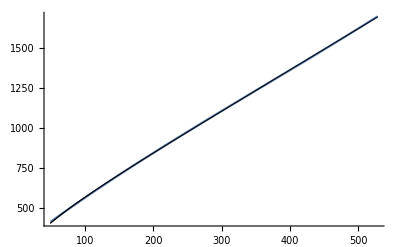

254.433+3.27305 P0-0.00199721 P0^2+1.8511×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em8=fitted
```

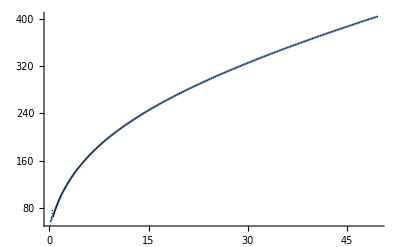

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em8=fitted;
```

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em8=fitted
```

-Graphics-

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em8=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

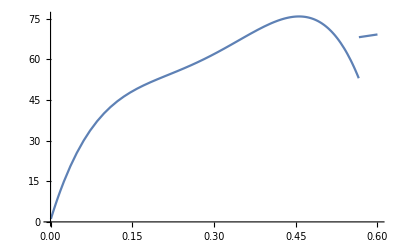

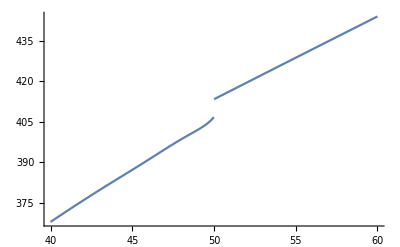

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em8;
FED2[P0_]=fitOuterCoreGUP1Em8;
FED3[P0_]=fitInnerCrustGUP1Em8;
FED4[P0_]=fitOuterCrustGUP1Em8;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,40,60},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em8//FortranForm
```

254.4326946197094 + 3.273054555571265*P0 - 
     -  0.001997209235201455*P0**2 + 1.8511002328575014e-6*P0**3

```mathematica
fitOuterCoreGUP1Em8//FortranForm
```

51.10109700227411 + 29.580374705635396*P0 + 
     -  2.5360966788240358*P0**2 - 3.362836320363709*P0**3 + 
     -  1.12655537724854*P0**4 - 0.21779082662158694*P0**5 + 
     -  0.027827189694289194*P0**6 - 0.0024904123035993414*P0**7 + 
     -  0.00016113623644452586*P0**8 - 
     -  7.669365209845754e-6*P0**9 + 2.703760430552597e-7*P0**10 - 
     -  7.041397888169705e-9*P0**11 + 
     -  1.3364159259686347e-10*P0**12 - 
     -  1.796211510388538e-12*P0**13 + 
     -  1.6192894869877814e-14*P0**14 - 
     -  8.779938560531548e-17*P0**15 + 
     -  2.1637379362009355e-19*P0**16

```mathematica
fitInnerCrustGUP1Em8//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 
     -  3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 
     -  7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em8//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

### fitting energy density GUP 1Em9

#### Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_G3Crust.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCrust=data[[1;;LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&]]];
```

```mathematica
dataInnerCrust=data[[LengthWhile[Transpose[data][[1]],#<5.0*10^(-4)&];;LengthWhile[Transpose[data][[1]],#<.5658&](*Dimensions[data][[1]]*)]];
```

#### GUP 1Em9 + Crust

```mathematica
fname=FileNameJoin[{NotebookDirectory[],"efpc_gup1E-9.dat"}];
data=ReadList[fname,{Number,Number}];
```

```mathematica
dataOuterCore=data[[LengthWhile[Transpose[data][[1]],#<0.5658&]+1;;LengthWhile[Transpose[data][[1]],#<50.&]]];
```

```mathematica
dataInnerCore=data[[LengthWhile[Transpose[data][[1]],#<50.&]+1;;Dimensions[data][[1]]]];
```

```mathematica
tambah1={dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-4]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-3]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-2]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-1]],dataInnerCrust[[Dimensions[dataInnerCrust][[1]]-0]]};
```

```mathematica
tambah2={(*dataOuterCore[[1]],dataOuterCore[[2]]*)};
```

```mathematica
dataOuterCoreNew=Join[tambah1,dataOuterCore];
```

```mathematica
dataInnerCrustNew=Join[dataInnerCrust,tambah2];
```

#### fitting

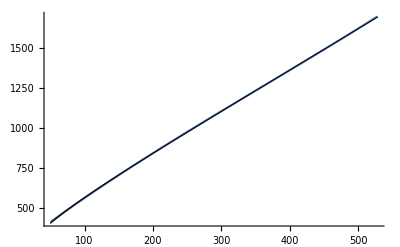

254.559+3.27234 P0-0.00199093 P0^2+1.84466×10^-6 P0^3

```mathematica
fitted=Fit[dataInnerCore,{1,P0,P0^2,P0^3},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCore][[1]]],Max[Transpose[dataInnerCore][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCore]}]
fitInnerCoreGUP1Em9=fitted
```

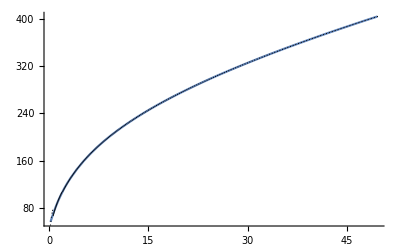

```mathematica
fitted=Fit[dataOuterCoreNew,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6,P0^7,P0^8,P0^9,P0^10,P0^11,P0^12,P0^13,P0^14,P0^15,P0^16},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCoreNew][[1]]],Max[Transpose[dataOuterCoreNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCoreNew]}]
fitOuterCoreGUP1Em9=fitted;
```

```mathematica
fitted=Fit[dataInnerCrustNew,{1,P0,P0^2,P0^3,P0^4(*,P0^5,P0^6,P0^7*)},P0];
Plot[fitted,{P0,Min[Transpose[dataInnerCrustNew][[1]]],Max[Transpose[dataInnerCrustNew][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataInnerCrustNew]}]
fitInnerCrustGUP1Em9=fitted
```

-Graphics-

0.659656+658.782 P0-3385.41 P0^2+8513.26 P0^3-7598.18 P0^4

```mathematica
fitted=Fit[dataOuterCrust,{1,P0,P0^2,P0^3,P0^4,P0^5,P0^6},P0];
Plot[fitted,{P0,Min[Transpose[dataOuterCrust][[1]]],Max[Transpose[dataOuterCrust][[1]]]},Epilog->{PointSize[0.002],Map[Point,dataOuterCrust]}]
fitOuterCrustGUP1Em9=fitted
```

-Graphics-

0.000233609+963.968 P0-6.02229×10^6 P0^2+3.89592×10^10 P0^3-1.29911×10^14 P0^4+2.09771×10^17 P0^5-1.29719×10^20 P0^6

#### Cek hasilnya

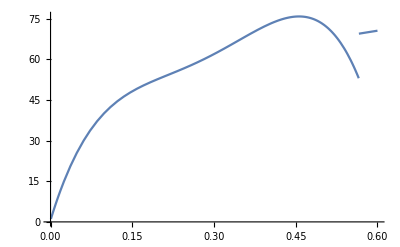

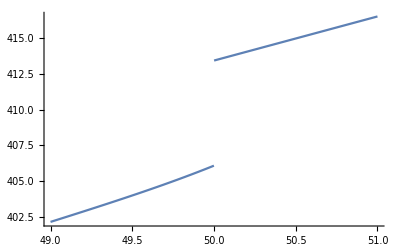

```mathematica
(* Model Neutron Star *)
FED1[P0_]=fitInnerCoreGUP1Em9;
FED2[P0_]=fitOuterCoreGUP1Em9;
FED3[P0_]=fitInnerCrustGUP1Em9;
FED4[P0_]=fitOuterCrustGUP1Em9;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.5658<p≤50.},{FED3[p],5.*10^(-4)<p≤0.5658}},FED4[p]]; (* Model Neutron Star *)
dpdϵ=1/D[ϵ[p],p];
Plot[ϵ[p],{p,0,.6}]
Plot[ϵ[p],{p,49,51},PlotRange->All]
```

#### Untuk ditulis di Fortran

```mathematica
fitInnerCoreGUP1Em9//FortranForm
```

254.5586443762641 + 3.272343184890167*P0 - 
     -  0.0019909310765835776*P0**2 + 1.8446607437157292e-6*P0**3

```mathematica
fitOuterCoreGUP1Em9//FortranForm
```

49.34701316942215 + 38.7432329585182*P0 - 
     -  6.0207597834429105*P0**2 + 0.5481717031310527*P0**3 + 
     -  0.06713032466584544*P0**4 - 0.031123560803850422*P0**5 + 
     -  0.005194256595745501*P0**6 - 0.0005321212341344053*P0**7 + 
     -  0.00003737764115198022*P0**8 - 
     -  1.8799322500754188e-6*P0**9 + 
     -  6.894328830278597e-8*P0**10 - 
     -  1.8492142295709409e-9*P0**11 + 
     -  3.5904038579625506e-11*P0**12 - 
     -  4.913125460512138e-13*P0**13 + 
     -  4.493677323677699e-15*P0**14 - 
     -  2.4654561028157746e-17*P0**15 + 
     -  6.135518282983326e-20*P0**16

```mathematica
fitInnerCrustGUP1Em9//FortranForm
```

0.6596556980482654 + 658.7820465828245*P0 - 
     -  3385.412057495701*P0**2 + 8513.26060947245*P0**3 - 
     -  7598.179318111917*P0**4

```mathematica
fitOuterCrustGUP1Em9//FortranForm
```

0.00023360915782327885 + 963.9682663375576*P0 - 
     -  6.022287440793628e6*P0**2 + 3.8959199862096825e10*P0**3 - 
     -  1.299108445236239e14*P0**4 + 2.097713931761943e17*P0**5 - 
     -  1.297185952864878e20*P0**6

## Tes

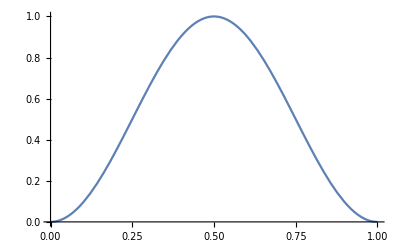

```mathematica
Plot[Sin[π x]^2,{x,0,1}]
```

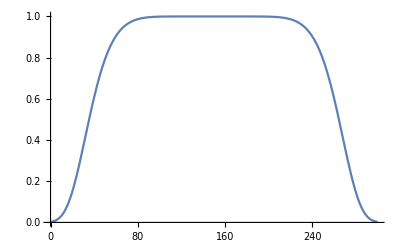

```mathematica
Plot[Exp[-(x-300/2)^8/(300/2.5)^8],{x,0,300},PlotRange->All]
```